Code by - Prashant Chauhan - This Program calculates the superconducting gap using exact method given in Tinkham book pg .. 63. Then it also caculates the relative penetration depth

Specify the Δ(0) and T_c

```mathematica
Tc=8;d0=0.001225;
```

Solving for Δ (T) using approximate method.

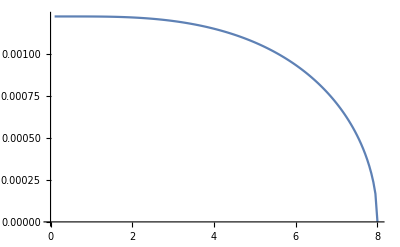

```mathematica
d[T_]:= d0*Tanh[1.74*√(Tc/T-1)]; data=Table[{T,d[T]},{T,0.1,Tc,0.05}] ;ListPlot[data,Joined->True]
```

Solving for Δ (T) using exact method.
Note:  d=(Δ (T))/(2 K_B T_c),(Δ (0))/(2 K_B T_c)=1.764/2, E=e/(2 K_B T_c), 1/(N(0)V)=1/0.3

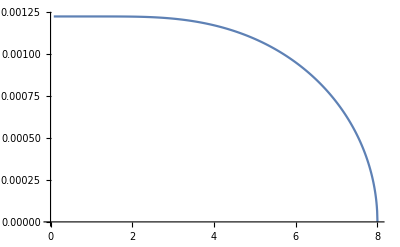

```mathematica
f[d_?NumericQ]:=NIntegrate[Tanh[(√(e^2+d^2))/T]/(√(e^2+d^2)),{e,0,12.36},Method->{"GaussKronrodRule","GaussPoints"->15},MaxRecursion->18,WorkingPrecision->15];
delta=ParallelTable[{T Tc,Quiet[(2 d d0)/1.764/.FindRoot[f[d]==1/0.3,{d,1}]]},{T,0.01,1,0.001}];m=Dimensions[delta]⟦1⟧;
ListPlot[delta,Joined->True]
```

1/λ_rel^2=Δ_rel^2 Tanh[(Δ (T))/(2 K_B T)]→ plot given below

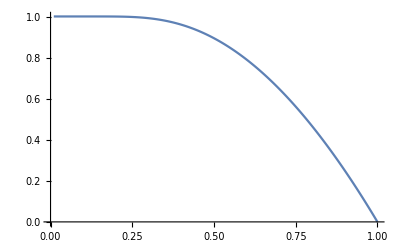

```mathematica
nrmpdin= Table[{delta⟦i,1⟧/Tc,(delta⟦i,2⟧ Tanh[(delta⟦i,2⟧ (1.764 Tc))/(delta⟦i,1⟧ (2 d0))])/d0},{i,m}];ListPlot[nrmpdin,Joined->True]
```

λ_rel=1/(√(Δ_rel^2 Tanh[(Δ (T))/(2 K_B T)]))→ plot given below

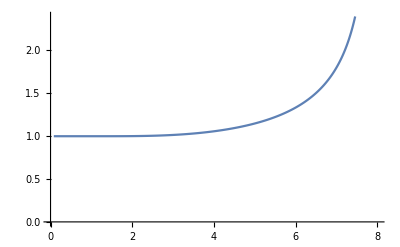

```mathematica
nrmpd=Table[{delta⟦i,1⟧,1/(√((delta⟦i,2⟧ Tanh[(delta⟦i,2⟧ (1.764 Tc))/(delta⟦i,1⟧ (2 d0))])/d0))},{i,m}];ListPlot[normpendepth,Joined->True]
```